# Plot

## Setup

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
rootdir = Directory[];

(* ----------------------------SCEGLIERE LAMBDA (10, 20 o 50) ------------------------ *)
lambda = 50;

dir =Switch[lambda, 10, SetDirectory["./lambda_10"], 20, SetDirectory["./lambda_20"], 50, SetDirectory["./lambda_50"]];
SetDirectory[dir];
Directory[]

imgsize = Large;
```

/media/matteo/data0/MC2.temp/lambda_50

```mathematica
data = Chop[Import["./export/2D.dat"],10^-5];
databeam = Import["./export/beam.dat"];
databeamray = Import["./export/beam_rayleigh.dat"];
mybeam = Import["./export/my_beam.dat"];

{Nr, Nc} =Dimensions[databeam]
```

{2601,8}

```mathematica
Dimensions[data]
```

{2601,8}

```mathematica
plot1 :=
ListPlot3D[
Table[
Transpose[{data[[All, 1]], data[[All, 2]], data[[All, i]]}],
{i, 3, Nc}
],
 AxesLabel->{"k_1 [m^-1]", "k_2 [m^-1]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->imgsize,  ImageSize->Large, PlotLabel->"2D dispersion surfaces",BoxRatios->{1, 1, 2}, PlotStyle->Automatic,
PlotTheme->"Scientific"
];
plot2 := 
ListPlot3D[
Table[
Transpose[{databeam[[All, 1]], databeam[[All, 2]], databeam[[All, i]]}]
,
 {i, 3,Nc}],
 AxesLabel->{"k_1 [m^-1]", "k_2 [m^-1]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->imgsize,  ImageSize->Large, PlotLabel->"E-B beam dispersion surfaces",BoxRatios->{1, 1, 2}, PlotStyle->Automatic,
PlotTheme->"Scientific"
];
plot3 := ListPlot3D[
Table[
Transpose[{databeamray[[All, 1]], databeamray[[All, 2]], databeamray[[All, i]]}]
,
 {i, 3,Nc}],
 AxesLabel->{"k_1 [m^-1]", "k_2 [m^-1]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->imgsize,  ImageSize->Large, PlotLabel->"Rayleigh beam dispersion surfaces",BoxRatios->{1, 1, 2},
PlotTheme->"Scientific"
];
plot4 := ListPlot3D[
Table[
Transpose[{mybeam[[All, 1]], mybeam[[All, 2]], mybeam[[All, i]]}]
,
 {i, 3,Nc}],
 AxesLabel->{"k_1 [m^-1]", "k_2 [m^-1]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->imgsize,  ImageSize->Large, PlotLabel->"My E-B beam dispersion surfaces",BoxRatios->{1, 1, 2},
PlotTheme->"Scientific"
];

Grid[{{plot1,plot2},{plot3,plot4}}]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

```mathematica
imgsize = 500;
k0=.;
k=.;
plot5[k0_, k_]:= Show[
ListPlot3D[
Table[
Transpose[{data[[All, 1]], data[[All, 2]], data[[All, i]]}]
,
 {i, k0,k}],
 AxesLabel->{"k_1 [m]", "k_2 [m]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->imgsize,  PlotLabel->"Dispersion surfaces", PlotStyle->Green,
PlotLegends->{"2D"},
PlotRange->Full,
PlotTheme->"Scientific"
],
ListPlot3D[
Table[
Transpose[{databeam[[All, 1]], databeam[[All, 2]], databeam[[All, i]]}]
,
 {i, k0,k}],
 AxesLabel->{"k_1 [m]", "k_2 [m]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->imgsize, PlotStyle->Automatic,
PlotLegends->{"E-B sliding grid"},
PlotRange->Full,
PlotTheme->"Scientific"
],
(*ListPlot3D[
Table[
Transpose[{databeamray[[All, 1]], databeamray[[All, 2]], databeamray[[All, i]]}]
,
 {i, k0,k}],
 AxesLabel->{"k_1 [m]", "k_2 [m]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->imgsize,  PlotLabel->"Dispersion surfaces", PlotStyle->Red,
PlotLegends->{"Beam Rayleigh"},
PlotRange->Full,
PlotTheme->"Scientific"
],*)
ListPlot3D[
Table[
Transpose[{mybeam[[All, 1]], mybeam[[All, 2]], mybeam[[All, i]]}]
,
 {i, k0,k}],
 AxesLabel->{"k_1 [m]", "k_2 [m]","ω/ω_ref [-]" }, Mesh->Automatic, ImageSize->imgsize,  ImageSize->Large, PlotStyle->Magenta,
PlotLegends->{"E-B beam"},
PlotRange->Full,
PlotTheme->"Scientific"
],
 PlotLabel->Text[Style["Dispersion surfaces " <>ToString[k-2], FontSize->16]],
BoxRatios->{1, 1, 2}
];

Table[plot5[i,i], {i, 3, Nc}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

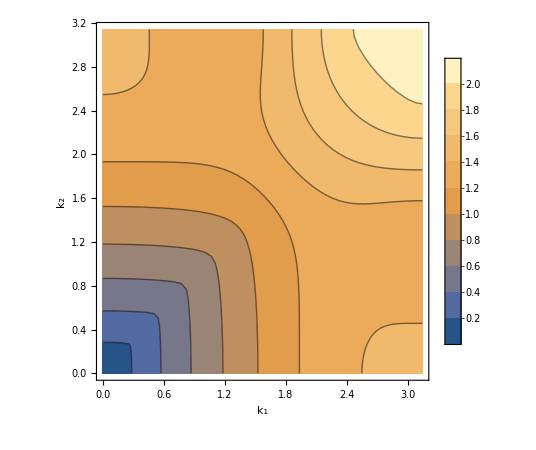
-Graphics3D- | -Graphics-

```mathematica
data0=databeam;
k = 2; 

Grid[
{{
ListPlot3D[
Transpose[{data0[[All, 1]], data0[[All, 2]], data0[[All, 2+k]]}],
AxesLabel->{"k_1", "k_2", "ω/ω_ref"},
ImageSize->imgsize,
BoxRatios->{1,1,2},
AxesOrigin->{0,0,0}
],
ListContourPlot[
Transpose[{data0[[All, 1]], data0[[All, 2]], data0[[All, 2+k]]}],
FrameLabel->{"k_1", "k_2"},
Contours->10,
PlotLegends-> Automatic,
ImageSize->imgsize
]
}}
]
```

```mathematica
Table[(data[[-1,i]]-databeam[[-1,i]])/data[[-1,i]]*100, {i, 3, Nc}];
Chop[Mean[data-databeam], 10^-5][[3;;]]
StandardDeviation[data-databeam][[3;;]]
```

{0.0602824,0.139297,0.0711488,0.0562785,-0.155165,-0.114674}

{0.0585169,0.0591247,0.104659,0.0679231,0.305287,0.319617}

```mathematica
Mean[Abs[data-mybeam]]
StandardDeviation[Abs[data-mybeam]]
```

{0.,0.,0.074575,0.139195,0.100023,0.0646353,0.251543,0.244648}

{0.,0.,0.0386092,0.059042,0.07732,0.058831,0.234376,0.239882}

```mathematica
data[[;;50, 4]]
```

{0,0.0501793,0.100328,0.150415,0.200409,0.250279,0.299991,0.349512,0.398808,0.447843,0.496578,0.544976,0.592994,0.64059,0.687717,0.73433,0.780376,0.825805,0.870559,0.914581,0.957811,1.00019,1.04164,1.08211,1.12153,1.15983,1.19694,1.23279,1.26733,1.3005,1.33222,1.36247,1.39119,1.41834,1.44389,1.46784,1.49015,1.51082,1.52986,1.54728,1.56308,1.57728,1.58991,1.60098,1.5948,1.58463,1.57617,1.56948,1.56465,1.56173}

```mathematica
diff1=Transpose@Prepend[{Chop[Mean[data-databeam], 10^-5][[3;;]],StandardDeviation[data-databeam][[3;;]],Chop[Mean[data-mybeam], 10^-5][[3;;]],StandardDeviation[data-mybeam][[3;;]]}, Transpose[Table[i, {i, 1, 6}]]];
title1="Media e deviazione standard della differenza tra le superfici di dispersione (ω/ω_ref)";
head1={{},{"Mode", "Mean(2D-SG)","Std(2D-SG)", "Mean(2D-EB)","Std(2D-EB)"}};


(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center, TableSpacing->{1.5,5}]}},
Dividers->None]&@@@{{title1,diff1, head1}})[[1]]
```

Thread::tdlen: Objects of unequal length in {{0,0,0,0,0.587885,0.587916,0.775622,1.29502},{0,0.15708,0.0058455,0.112747,0.584725,0.593844,0.77884,1.29535},{0,0.314159,0.0117389,0.217961,0.575863,0.61392,0.787868,1.29637},«5»,{0,1.25664,0.0503152,0.451102,0.471629,0.892357,1.16574,1.31785},{0,1.41372,0.0574907,0.452531,0.456559,0.910579,1.2876,1.3242},«431»}+{«1»} cannot be combined.

Thread::tdlen: Objects of unequal length in {{0,0,0,0,0.587885,0.587916,0.775622,1.29502},{0,0.15708,0.0058455,0.112747,0.584725,0.593844,0.77884,1.29535},{0,0.314159,0.0117389,0.217961,0.575863,0.61392,0.787868,1.29637},«5»,{0,1.25664,0.0503152,0.451102,0.471629,0.892357,1.16574,1.31785},{0,1.41372,0.0574907,0.452531,0.456559,0.910579,1.2876,1.3242},«431»}+{{0,0,0,0,-0.550551,-0.550551,-0.789257,-1.23274},«9»,«2591»} cannot be combined.

Part::take: Cannot take positions 3 through -1 in Mean[{{0,0,0,0,0.587885,0.587916,0.775622,1.29502},{0,0.15708,0.0058455,0.112747,0.584725,0.593844,0.77884,1.29535},{0,0.314159,0.0117389,0.217961,0.575863,0.61392,0.787868,1.29637},«5»,{0,1.25664,0.0503152,0.451102,0.471629,0.892357,1.16574,1.31785},{0,1.41372,0.0574907,0.452531,0.456559,0.910579,1.2876,1.3242},«431»}+{{0,0,0,0,-0.550551,-0.550551,-0.789257,-1.23274},«9»,«2591»}].

Thread::tdlen: Objects of unequal length in {{0,0,0,0,0.587885,0.587916,0.775622,1.29502},{0,0.15708,0.0058455,0.112747,0.584725,0.593844,0.77884,1.29535},{0,0.314159,0.0117389,0.217961,0.575863,0.61392,0.787868,1.29637},«5»,{0,1.25664,0.0503152,0.451102,0.471629,0.892357,1.16574,1.31785},{0,1.41372,0.0574907,0.452531,0.456559,0.910579,1.2876,1.3242},«431»}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::take: Cannot take positions 3 through -1 in StandardDeviation[{{0,0,0,0,0.587885,0.587916,0.775622,1.29502},{0,0.15708,0.0058455,0.112747,0.584725,0.593844,0.77884,1.29535},{0,0.314159,0.0117389,0.217961,0.575863,0.61392,0.787868,1.29637},«5»,{0,1.25664,0.0503152,0.451102,0.471629,0.892357,1.16574,1.31785},{0,1.41372,0.0574907,0.452531,0.456559,0.910579,1.2876,1.3242},«431»}+{«1»}].

Part::take: Cannot take positions 3 through -1 in Mean[{{0,0,0,0,0.587885,0.587916,0.775622,1.29502},{0,0.15708,0.0058455,0.112747,0.584725,0.593844,0.77884,1.29535},{0,0.314159,0.0117389,0.217961,0.575863,0.61392,0.787868,1.29637},«5»,{0,1.25664,0.0503152,0.451102,0.471629,0.892357,1.16574,1.31785},{0,1.41372,0.0574907,0.452531,0.456559,0.910579,1.2876,1.3242},«431»}+{{0,0,0,0,-0.550558,-0.550558,-0.789575,-1.23343},«9»,«2591»}].

General::stop: Further output of Part::take will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{1,2,3,4,5,6},Mean[{«1»}+{«1»}]⟦3;;All⟧,StandardDeviation[«1»]⟦«1»⟧,Mean[{«1»}+{«1»}]⟦3;;All⟧,StandardDeviation[{{0,0,0,0,0.587885,0.587916,0.775622,1.29502},{0,0.15708,0.0058455,0.112747,0.584725,0.593844,0.77884,1.29535},{0,0.314159,0.0117389,0.217961,0.575863,0.61392,0.787868,1.29637},«5»,{0,1.25664,0.0503152,0.451102,0.471629,0.892357,1.16574,1.31785},{0,1.41372,0.0574907,0.452531,0.456559,0.910579,1.2876,1.3242},«431»}+{«1»}]⟦3;;All⟧} cannot be transposed.

Media e deviazione standard della differenza tra le superfici di dispersione (ω/ω_ref)
Transpose[{{1,2,3,4,5,6},3,StandardDeviation[{{0,0,0,0,0.587885,0.587916,0.775622,1.29502},{0,0.15708,0.0058455,0.112747,0.584725,0.593844,0.77884,1.29535},{0,0.314159,0.0117389,0.217961,0.575863,0.61392,0.787868,1.29637},436,{3.14159,2.98451,0.197324,0.478339,1.21038,1.2113,1.7162,2.4739},{3.14159,3.14159,0.196549,0.478366,1.2119,1.21196,1.71444,2.47768}}+1]⟦3;;All⟧}]
 |  |  |  |

```mathematica
diff2=Transpose@Prepend[{Table[(data[[-1,i]]-databeam[[-1,i]])/data[[-1,i]]*100, {i, 3, Nc}],Table[(data[[-1,i]]-mybeam[[-1,i]])/data[[-1,i]]*100, {i, 3, Nc}]}, Transpose[Table[i, {i, 1, 6}]]];
title2="Differenza percentuale del modello 2D con i modelli beam per {k_1,k_2}={π,π} (ω/ω_ref)";
head2={{},{"Mode", "2D-SG [%]","2D-EB [%]"}};


(Grid[{
{Item[#1,Alignment->Center]},
{TableForm[#2,TableHeadings->#3, TableAlignments->Center, TableSpacing->{1.5,10}]}},
Dividers->None]&@@@{{title2,diff2, head2}})[[1]]
```

Differenza percentuale del modello 2D con i modelli beam per {k_1,k_2}={π,π} (ω/ω_ref)
 | Mode | 2D-SG [%] | 2D-EB [%]
 | 1 | -0.428721 | -0.428773
 | 2 | 6.45951 | 6.463
 | 3 | 3.96285 | 3.91403
 | 4 | 3.96746 | 3.91865
 | 5 | -3.62135 | -3.62567
 | 6 | 2.40596 | 2.40233